```mathematica
Plot3D[{Sin[x+y^2],-0.99},{x,-2,2},{y,-2,2},Filling->Bottom,RegionFunction->(#1^2+#2^2<3&),Axes->False,Boxed->False,ImageSize->600]
```

-Graphics3D-

```mathematica
nodes=
{
	{-3,3},{-1,3},{1 ,3},{3,3},
	{-3,1 },{-1,1},{1 ,1},{3,1 },
	{-3,-1},{-1,-1},{1 ,-1},{3,-1},
	{-3,-3},{-1,-3},{1 ,-3},{3,-3}
};
nodesT={
	{-3,3},{-0.3,3},{1.5,3},{3,3},
	{-3,2.1},{-0.3,0.6},{0.9,0.9},{3,1.2},
	{-3,-0.9},{-0.9,-0.9},{1.2,-1.2},{3,-0.6},
	{-3,-3},{-0.6,-3},{4.2,-3},{3,-3}
};
nodesG=Insert[nodes,1,Table[{i,3},{i,1,16}]];
nodesH=Insert[nodes,0,Table[{i,3},{i,1,16}]];
nodesGT=Insert[nodesT,1,Table[{i,3},{i,1,16}]];
nodesHT=Insert[nodesT,0,Table[{i,3},{i,1,16}]];
nodesMidG={nodesG[[6]],nodesG[[7]],nodesG[[10]],nodesG[[11]]};
nodesMidH={nodesH[[6]],nodesH[[7]],nodesH[[10]],nodesH[[11]]};
nodesMidHT={nodesHT[[6]],nodesHT[[7]],nodesHT[[10]],nodesHT[[11]]};
nodesMidGT={nodesGT[[6]],nodesGT[[7]],nodesGT[[10]],nodesGT[[11]]};
lines={
	Line[{nodes[[5]],nodes[[6]],nodes[[7]],nodes[[8]]}],
	Line[{nodes[[9]],nodes[[10]],nodes[[11]],nodes[[12]]}],
	Line[{nodes[[13]],nodes[[14]],nodes[[15]],nodes[[16]],
		nodes[[12]],nodes[[8]],nodes[[4]],nodes[[3]],nodes[[2]],nodes[[1]],nodes[[5]],nodes[[9]],nodes[[13]]}],
	Line[{nodes[[2]],nodes[[6]],nodes[[10]],nodes[[14]]}],
	Line[{nodes[[3]],nodes[[7]],nodes[[11]],nodes[[15]]}]
};
linesT={
	Line[{nodesT[[5]],nodesT[[6]],nodesT[[7]],nodesT[[8]]}],
	Line[{nodesT[[9]],nodesT[[10]],nodesT[[11]],nodesT[[12]]}],
	Line[{nodesT[[13]],nodesT[[14]],nodesT[[15]],nodesT[[16]],
		nodesT[[12]],nodesT[[8]],nodesT[[4]],nodesT[[3]],nodesT[[2]],nodesT[[1]],nodesT[[5]],nodesT[[9]],nodesT[[13]]}],
	Line[{nodesT[[2]],nodesT[[6]],nodesT[[10]],nodesT[[14]]}],
	Line[{nodesT[[3]],nodesT[[7]],nodesT[[11]],nodesT[[15]]}]
};
floorLines={
	Line[{nodesH[[5]],nodesH[[6]],nodesH[[7]],nodesH[[8]]}],
	Line[{nodesH[[9]],nodesH[[10]],nodesH[[11]],nodesH[[12]]}],
	Line[{nodesH[[13]],nodesH[[14]],nodesH[[15]],nodesH[[16]],
		nodesH[[12]],nodesH[[8]],nodesH[[4]],nodesH[[3]],nodesH[[2]],nodesH[[1]],nodesH[[5]],nodesH[[9]],nodesH[[13]]}],
	Line[{nodesH[[2]],nodesH[[6]],nodesH[[10]],nodesH[[14]]}],
	Line[{nodesH[[3]],nodesH[[7]],nodesH[[11]],nodesH[[15]]}]
};
floorLinesT={
	Line[{nodesHT[[5]],nodesHT[[6]],nodesHT[[7]],nodesHT[[8]]}],
	Line[{nodesHT[[9]],nodesHT[[10]],nodesHT[[11]],nodesHT[[12]]}],
	Line[{nodesHT[[13]],nodesHT[[14]],nodesHT[[15]],nodesHT[[16]],
		nodesHT[[12]],nodesHT[[8]],nodesHT[[4]],nodesHT[[3]],nodesHT[[2]],nodesHT[[1]],nodesHT[[5]],nodesHT[[9]],nodesHT[[13]]}],
	Line[{nodesHT[[2]],nodesHT[[6]],nodesHT[[10]],nodesHT[[14]]}],
	Line[{nodesHT[[3]],nodesHT[[7]],nodesHT[[11]],nodesHT[[15]]}]
};
ceilingLines={
	Line[{nodesG[[5]],nodesG[[6]],nodesG[[7]],nodesG[[8]]}],
	Line[{nodesG[[9]],nodesG[[10]],nodesG[[11]],nodesG[[12]]}],
	Line[{nodesG[[13]],nodesG[[14]],nodesG[[15]],nodesG[[16]],
		nodesG[[12]],nodesG[[8]],nodesG[[4]],nodesG[[3]],nodesG[[2]],nodesG[[1]],nodesG[[5]],nodesG[[9]],nodesG[[13]]}],
	Line[{nodesG[[2]],nodesG[[6]],nodesG[[10]],nodesG[[14]]}],
	Line[{nodesG[[3]],nodesG[[7]],nodesG[[11]],nodesG[[15]]}]
};
g[x_,y_,x0_,y0_,σ_]:=Exp[-((x-x0)^2+(y-y0)^2)/(2 σ^2)]    (* Custom 2D Gaussian *)
nXYGridLines=4;
xYGridLines=Table[{6/(nXYGridLines-1) i-3,Thickness[0.002]} , {i,0,nXYGridLines-1}]
nXZGridLines=3;
xZGridLines=Table[{1/(nXZGridLines-1) i,Thickness[0.002] }, {i,0,nXZGridLines-1}]
nZXGridLines=4;
zXGridLines=Table[{6/(nZXGridLines-1) i-3,Directive[Thickness[0.003],Black]}, {i,0,nZXGridLines-1}]     (* Grid line positions and their individual stylings for the lower plate on the 3D plot. *)
plotVisuals={Lighting["Neutral"],Specularity[White,70],Opacity[0.6]};
plotOptions={Mesh->{4,4},MeshStyle->Thickness[0.0015]};
stds={0.72,0.72,0.72,0.72};
```

{{-3,Thickness[0.002]},{-1,Thickness[0.002]},{1,Thickness[0.002]},{3,Thickness[0.002]}}

{{0,Thickness[0.002]},{1/2,Thickness[0.002]},{1,Thickness[0.002]}}

{{-3,Directive[Thickness[0.003],GrayLevel[0]]},{-1,Directive[Thickness[0.003],GrayLevel[0]]},{1,Directive[Thickness[0.003],GrayLevel[0]]},{3,Directive[Thickness[0.003],GrayLevel[0]]}}

```mathematica
SetOptions[Plot3D,
	AxesLabel->Automatic,
	PlotRange->{{-3,3},{-3,3},{0,1}},
	PlotPoints->{100,100},
	LabelStyle->{FontFamily["DejaVu Math TeX Gyre"],Directive[20,Bold]},
	Ticks->{{-3,-1,1,3},{-3,-1,1,3},Automatic},
	Boxed->False
];
opacity = 0.6;
meshLineThickness=0.0035;
meshColors={Gray,Gray,Gray,Gray};
sufaceColors={Darker[Red],Blue,Green,Darker[Yellow]};

Show[
	Plot3D[
		g[x,y,nodes[[6,1]],nodes[[6,2]],stds[[1]]],
		{x,nodes[[6,1]]-2.7 stds[[1]],nodes[[6,1]]+2.7  stds[[1]]},
		{y,nodes[[6,2]]-2.7  stds[[1]],nodes[[6,2]]+2.7  stds[[1]]},
		Evaluate[plotOptions],
		PlotStyle->Directive[RGBColor["#ff8e8e"],plotVisuals],
		(*MeshShading->{{{sufaceColors[[1]],Opacity[opacity]},{sufaceColors[[1]],Opacity[opacity]}},{{sufaceColors[[1]],Opacity[opacity]},{sufaceColors[[1]],Opacity[opacity]}}},
		MeshStyle->{{Thickness[meshLineThickness],meshColors[[1]]}},*)
		RegionFunction->Function[{x,y,z},(x-nodes[[6,1]])^2+(y-nodes[[6,2]])^2<(2.7 stds[[1]])^2]
	],
	Plot3D[
		g[x,y,nodes[[7,1]],nodes[[7,2]],stds[[2]]],
		{x,nodes[[7,1]]-2.7 stds[[2]],nodes[[7,1]]+2.7 stds[[2]]},
		{y,nodes[[7,2]]-2.7 stds[[2]],nodes[[7,2]]+2.7 stds[[2]]},
		Evaluate[plotOptions],
		PlotStyle->Directive[RGBColor["#8beb91"],plotVisuals],
		(*MeshShading->{{{sufaceColors[[2]],Opacity[opacity]},{sufaceColors[[2]],Opacity[opacity]}},{{sufaceColors[[2]],Opacity[opacity]},{sufaceColors[[2]],Opacity[opacity]}}},
		MeshStyle->{{Thickness[meshLineThickness],meshColors[[2]]}},*)
		RegionFunction->Function[{x,y,z},(x-nodes[[7,1]])^2+(y-nodes[[7,2]])^2<(2.7 stds[[2]])^2]
	],
	Plot3D[
		g[x,y,nodes[[10,1]],nodes[[10,2]],stds[[3]]],
		{x,nodes[[10,1]]-2.7 stds[[3]],nodes[[10,1]]+2.7 stds[[3]]},
		{y,nodes[[10,2]]-2.7 stds[[3]],nodes[[10,2]]+2.7 stds[[3]]},
		Evaluate[plotOptions],
		PlotStyle->Directive[RGBColor["#66aaf6"],plotVisuals],
		RegionFunction->Function[{x,y,z},(x-nodes[[10,1]])^2+(y-nodes[[10,2]])^2<(2.7 stds[[3]])^2]
	],
	Plot3D[
		g[x,y,nodes[[11,1]],nodes[[11,2]],stds[[4]]],
		{x,nodes[[11,1]]-2.7 stds[[4]],nodes[[11,1]]+2.7 stds[[4]]},
		{y,nodes[[11,2]]-2.7 stds[[4]],nodes[[11,2]]+2.7 stds[[4]]},
		Evaluate[plotOptions],
		PlotStyle->Directive[RGBColor["#d5d87d"],plotVisuals],
		RegionFunction->Function[{x,y,z},(x-nodes[[11,1]])^2+(y-nodes[[11,2]])^2<(2.7 stds[[4]])^2]
	],
	Graphics3D[{
		Red,PointSize[0.03],Thickness[0.009],
		Table[Line[{nodesMidH[[i]],nodesMidG[[i]]}],{i,1,Length[nodesMidG]}],
		Point[nodesH],
		Black,Thickness[0.009],Specularity[White,70],
		floorLines,
		LightBlue, Opacity[0.1],
		Hyperplane[{1,0,0},{-3,0,0}],
		Hyperplane[{0,-1,0},{0,3,0}],
		RGBColor["#a4f2f1"], Opacity[0.5],
		Hyperplane[{0,0,1},{0,0,0}]
	}],
	ImageSize->680,
	FaceGrids->{
			{{-1,0,0},{xYGridLines,xZGridLines}},
			{{0,1,0},{xYGridLines,xZGridLines}}(*,
			{{0,0,-1},{zXGridLines,zXGridLines}}*)
	}
]
```

-Graphics3D-

```mathematica
plotOptions2={Mesh->{6,6},MeshStyle->Thickness[0.0015]};
plotVisuals2={Lighting["Neutral"],Specularity[GrayLevel[1],70],Opacity[0.6]};
Show[
	Plot3D[
		g[x,y,nodes[[6,1]],nodes[[6,2]],stds[[1]]]+
			g[x,y,nodes[[7,1]],nodes[[7,2]],stds[[2]]]+
			g[x,y,nodes[[10,1]],nodes[[10,2]],stds[[3]]] +
			g[x,y,nodes[[11,1]],nodes[[11,2]],stds[[4]]],
		{x,-3,3},
		{y,-3,3},
		Evaluate[plotOptions2],
		PlotStyle->Directive[RGBColor["#ff8e8e"],plotVisuals2],
		PlotRange->{{-3,3},{-3,3},{0,1.06}},
		Boxed->False
	],
	Graphics3D[{
		Red,PointSize[0.03],Thickness[0.009],
		Table[Line[{nodesMidH[[i]],nodesMidG[[i]]+{0,0,0.03}}],{i,1,Length[nodesMidG]}],
		Point[nodesH],
		Black,Thickness[0.009],Specularity[White,70],
		floorLines,
		LightBlue, Opacity[0.1],
		Hyperplane[{1,0,0},{-3,0,0}],
		Hyperplane[{0,-1,0},{0,3,0}],
		RGBColor["#a4f2f1"], Opacity[0.5],
		Hyperplane[{0,0,1},{0,0,0}]
	}],
	ImageSize->700,
	FaceGrids->{
			{{-1,0,0},{xYGridLines,xZGridLines}},
			{{0,1,0},{xYGridLines,xZGridLines}}(*,
			{{0,0,-1},{zXGridLines,zXGridLines}}*)
	}
]
```

-Graphics3D-

```mathematica
plotOptions3={Mesh->{3,3},MeshStyle->Thickness[0.0012]};
plotVisuals3={Lighting["Neutral"],Specularity[GrayLevel[1],70],Opacity[0.75]};
Show[
	Plot3D[
		g[x,y,nodes[[6,1]],nodes[[6,2]],stds[[1]]],
		{x,nodes[[6,1]]-2.7 stds[[1]],nodes[[6,1]]+2.7  stds[[1]]},
		{y,nodes[[6,2]]-2.7  stds[[1]],nodes[[6,2]]+2.7  stds[[1]]},
		Evaluate[plotOptions3],
		PlotStyle->Directive[RGBColor["#ff8e8e"],plotVisuals3],
		RegionFunction->Function[{x,y,z},(x-nodes[[6,1]])^2+(y-nodes[[6,2]])^2<(2.7 stds[[1]])^2 && x>-1 && y<1 ]
	],
	Plot3D[
		g[x,y,nodes[[7,1]],nodes[[7,2]],stds[[2]]],
		{x,nodes[[7,1]]-2.7 stds[[2]],nodes[[7,1]]+2.7 stds[[2]]},
		{y,nodes[[7,2]]-2.7 stds[[2]],nodes[[7,2]]+2.7 stds[[2]]},
		Evaluate[plotOptions3],
		PlotStyle->Directive[RGBColor["#8beb91"],plotVisuals3],
		RegionFunction->Function[{x,y,z},(x-nodes[[7,1]])^2+(y-nodes[[7,2]])^2<(2.7 stds[[2]])^2&& x<1 && y<1]
	],
	Plot3D[
		g[x,y,nodes[[10,1]],nodes[[10,2]],stds[[3]]],
		{x,nodes[[10,1]]-2.7 stds[[3]],nodes[[10,1]]+2.7 stds[[3]]},
		{y,nodes[[10,2]]-2.7 stds[[3]],nodes[[10,2]]+2.7 stds[[3]]},
		Evaluate[plotOptions3],
		PlotStyle->Directive[RGBColor["#66aaf6"],plotVisuals3],
		RegionFunction->Function[{x,y,z},(x-nodes[[10,1]])^2+(y-nodes[[10,2]])^2<(2.7 stds[[3]])^2 && x>-1 && y>-1]
	],
	Plot3D[
		g[x,y,nodes[[11,1]],nodes[[11,2]],stds[[4]]],
		{x,nodes[[11,1]]-2.7 stds[[4]],nodes[[11,1]]+2.7 stds[[4]]},
		{y,nodes[[11,2]]-2.7 stds[[4]],nodes[[11,2]]+2.7 stds[[4]]},
		Evaluate[plotOptions3],
		PlotStyle->Directive[RGBColor["#d5d87d"],plotVisuals3],
		RegionFunction->Function[{x,y,z},(x-nodes[[11,1]])^2+(y-nodes[[11,2]])^2<(2.7 stds[[4]])^2 && x<1  && y>-1]
	],
	Graphics3D[{
		Red,PointSize[0.03],Thickness[0.009],
		Table[Line[{nodesMidH[[i]],nodesMidG[[i]]}],{i,1,Length[nodesMidG]}],
		Point[nodesH],
		Black,Thickness[0.009],Specularity[White,70],
		floorLines,
		LightBlue, Opacity[0.1],
		Hyperplane[{1,0,0},{-3,0,0}],
		Hyperplane[{0,-1,0},{0,3,0}],
		RGBColor["#a4f2f1"], Opacity[0.5],
		Hyperplane[{0,0,1},{0,0,0}]
	}],
	ImageSize->670,
	FaceGrids->{
			{{-1,0,0},{xYGridLines,xZGridLines}},
			{{0,1,0},{xYGridLines,xZGridLines}}(*,
			{{0,0,-1},{zXGridLines,zXGridLines}}*)
	}
]
```

-Graphics3D-

```mathematica
(* Quadrilateral shape functions.*)
nodesMidHTT={nodesMidHT[[3]],nodesMidHT[[4]],nodesMidHT[[2]],nodesMidHT[[1]]};
Subscript[S, 1][ξ_,η_]:= 1/4(1-ξ)(1-η)
Subscript[S, 2][ξ_,η_]:= 1/4(1+ξ)(1-η)
Subscript[S, 3][ξ_,η_]:= 1/4(1+ξ)(1+η)
Subscript[S, 4][ξ_,η_]:= 1/4(1-ξ)(1+η)
(* Transformation functions from fundamental square to deformed quadrilateral. *)
P[ξ_,η_]:= ∑_(i=1)^4 nodesMidHTT[[i,1]] Subscript[S, i][ξ,η]
Q[ξ_,η_]:= ∑_(i=1)^4 nodesMidHTT[[i,2]] Subscript[S, i][ξ,η]
Block[{ξ,η},
	ξ=1;
	η=0;
	{P[ξ,η],Q[ξ,η]}
]
```

{2.025,1.425}

```mathematica
plotVisuals4={Lighting["Neutral"],Specularity[GrayLevel[1],70],Opacity[0.6]};
Show[
	Plot3D[
		g[x,y,nodesT[[6,1]],nodesT[[6,2]],stds[[1]]],
		{x,nodesT[[6,1]]-2.7 stds[[1]],nodesT[[6,1]]+2.7  stds[[1]]},
		{y,nodesT[[6,2]]-2.7  stds[[1]],nodesT[[6,2]]+2.7  stds[[1]]},
		PlotStyle->Directive[RGBColor["#ff8e8e"],plotVisuals4],
		RegionFunction->Function[{x,y,z},(x-nodesT[[6,1]])^2+(y-nodesT[[6,2]])^2<(2.7 stds[[1]])^2]
	],
	Plot3D[
		g[x,y,nodesT[[7,1]],nodesT[[7,2]],stds[[2]]],
		{x,nodesT[[7,1]]-2.7 stds[[2]],nodesT[[7,1]]+2.7 stds[[2]]},
		{y,nodesT[[7,2]]-2.7 stds[[2]],nodesT[[7,2]]+2.7 stds[[2]]},
		PlotStyle->Directive[RGBColor["#8beb91"],plotVisuals4],
		RegionFunction->Function[{x,y,z},(x-nodesT[[7,1]])^2+(y-nodesT[[7,2]])^2<(2.7 stds[[2]])^2]
	],
	Plot3D[
		g[P[ξ,η],Q[ξ,η],0,0,stds[[3]]],
		{x,nodesT[[10,1]]-2.7 stds[[3]],nodesT[[10,1]]+2.7 stds[[3]]},
		{y,nodesT[[10,2]]-2.7 stds[[3]],nodesT[[10,2]]+2.7 stds[[3]]},
		PlotStyle->Directive[RGBColor["#66aaf6"],plotVisuals4],
		RegionFunction->Function[{x,y,z},(x-nodesT[[10,1]])^2+(y-nodesT[[10,2]])^2<(2.7 stds[[3]])^2]
	],
	Plot3D[
		g[x,y,nodesT[[11,1]],nodesT[[11,2]],stds[[4]]],
		{x,nodesT[[11,1]]-2.7 stds[[4]],nodesT[[11,1]]+2.7 stds[[4]]},
		{y,nodesT[[11,2]]-2.7 stds[[4]],nodesT[[11,2]]+2.7 stds[[4]]},
		PlotStyle->Directive[RGBColor["#d5d87d"],plotVisuals4],
		RegionFunction->Function[{x,y,z},(x-nodesT[[11,1]])^2+(y-nodesT[[11,2]])^2<(2.7 stds[[4]])^2]
	],
	Graphics3D[{
		Red,PointSize[0.03],Thickness[0.009],
		Table[Line[{nodesMidHT[[i]],nodesMidGT[[i]]}],{i,1,Length[nodesMidGT]}],
		Point[nodesHT],
		Black,Thickness[0.009],Specularity[White,70],
		floorLinesT,
		LightBlue, Opacity[0.1],
		Hyperplane[{1,0,0},{0,0,0}],
		Hyperplane[{0,-1,0},{0,3,0}],
		RGBColor["#a4f2f1"], Opacity[0.5],
		Hyperplane[{0,0,1},{0,0,0}]
	}],
	ImageSize->600,
	FaceGrids->{
			{{-1,0,0},{xYGridLines,xZGridLines}},
			{{0,1,0},{xYGridLines,xZGridLines}}(*,
			{{0,0,-1},{zXGridLines,zXGridLines}}*)
	}
]
```

-Graphics3D-

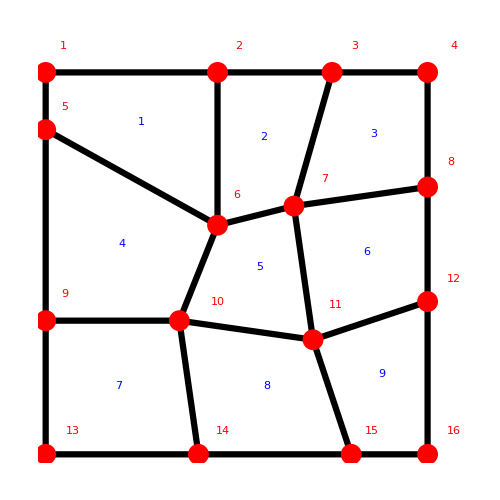

```mathematica
Graphics[{
	Black,Thickness[0.009],
	linesT,
	Red,PointSize[0.03],
	Point[nodesT],
	FontSize->36,Red,
	Text[13,{3 0.07,3 0.06}], Text[14,{3 0.465,3 0.06}], Text[15,{3 0.855,3 0.06}],Text[16,{3 1.07,3 0.06}],
	Text[9,{3 0.05,3 0.42}],Text[10,{3 0.45,3 0.40}],Text[11,{3 0.76,3 0.39}],Text[12,{3 1.07,3 0.46}],
	Text[5,{3 0.05,3 0.91}],Text[6,{3 0.50,3 0.68}],Text[7,{3 0.73,3 0.72}],Text[8,{3 1.06,3 0.765}],
	Text[1,{3 0.045,3 1.07}],Text[2,{3 0.505,3 1.07}],Text[3,{3 0.81,3 1.07}],Text[4,{3 1.07,3 1.07}],
	FontSize->70,Blue,
	Text[1,{3 0.25,3 0.87}],Text[2,{3 0.57,3 0.83}],Text[3,{3 0.86,3 0.84}],
	Text[4,{3 0.20,3 0.55}],Text[5,{3 0.56,3 0.49}],Text[6,{3 0.84,3 0.53}],
	Text[7,{3 0.19,3 0.18}],Text[8,{3 0.58,3 0.18}],Text[9,{3 0.88,3 0.21}]
},ImageSize->500]
```

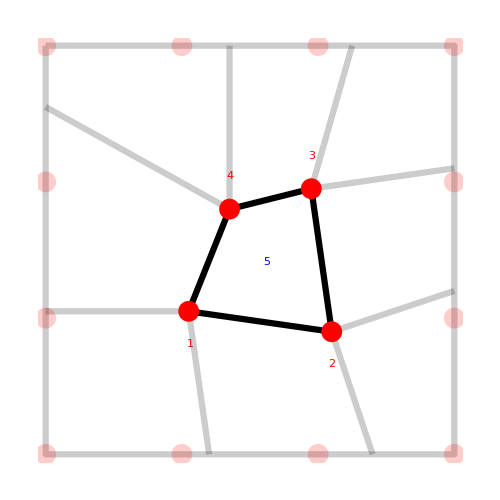

```mathematica
nodesMidT={nodesT[[6]],nodesT[[7]],nodesT[[10]],nodesT[[11]]};
nodesMid={nodes[[6]],nodes[[7]],nodes[[10]],nodes[[11]]};
otherNodes={nodes[[1]],nodes[[2]],nodes[[3]],nodes[[4]],nodes[[5]],nodes[[8]],nodes[[9]],nodes[[12]],nodes[[13]],nodes[[14]],nodes[[15]],nodes[[16]]};
otherNodesT={nodesT[[1]],nodesT[[2]],nodesT[[3]],nodesT[[4]],nodesT[[5]],nodesT[[8]],nodesT[[9]],nodesT[[12]],nodesT[[13]],nodesT[[14]],nodesT[[15]],nodesT[[16]]};
linesMid={Line[{nodes[[6]],nodes[[7]],nodes[[11]],nodes[[10]],nodes[[6]]}]};
linesMidT={Line[{nodesT[[6]],nodesT[[7]],nodesT[[11]],nodesT[[10]],nodesT[[6]]}]};
otherLines={
	Line[{nodes[[1]],nodes[[4]],nodes[[16]],nodes[[13]],nodes[[1]]}],
	Line[{nodes[[2]],nodes[[6]]}],
	Line[{nodes[[3]],nodes[[7]]}],
	Line[{nodes[[7]],nodes[[8]]}],
	Line[{nodes[[11]],nodes[[12]]}],
	Line[{nodes[[11]],nodes[[15]]}],
	Line[{nodes[[10]],nodes[[14]]}],
	Line[{nodes[[9]],nodes[[10]]}],
	Line[{nodes[[5]],nodes[[6]]}]
};
otherLinesT={
	Line[{nodesT[[1]],nodesT[[4]],nodesT[[16]],nodesT[[13]],nodesT[[1]]}],
	Line[{nodesT[[2]],nodesT[[6]]}],
	Line[{nodesT[[3]],nodesT[[7]]}],
	Line[{nodesT[[7]],nodesT[[8]]}],
	Line[{nodesT[[11]],nodesT[[12]]}],
	Line[{nodesT[[11]],nodesT[[15]]}],
	Line[{nodesT[[10]],nodesT[[14]]}],
	Line[{nodesT[[9]],nodesT[[10]]}],
	Line[{nodesT[[5]],nodesT[[6]]}]
};
Graphics[{
	Black,Thickness[0.009],
	linesMidT,
	Opacity[0.2],
	otherLinesT,
	Opacity[1.0],
	Red,PointSize[0.03],
	Point[nodesMidT],
	Opacity[0.2],
	Point[otherNodes],
	Opacity[1.0],FontSize->70,Blue,
	Text[5,{3 0.54,3 0.47}],
	FontSize->42,Red,
	Text[4,{3 0.45,3 0.68}],Text[3,{3 0.65,3 0.73}],Text[1,{3 0.355,3 0.27}],Text[2,{3 0.70,3 0.22}]
	},
	ImageSize->500]
```

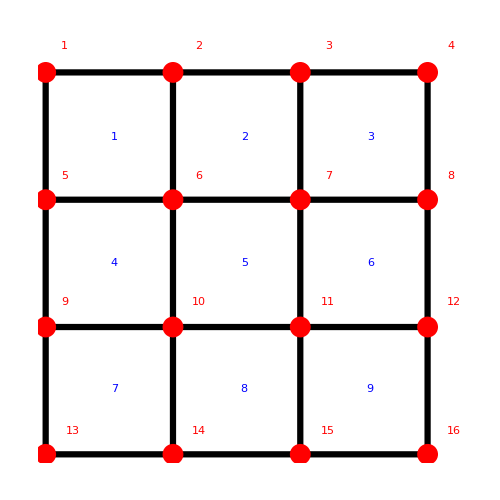

```mathematica
Graphics[{
	Black,Thickness[0.009],
	lines,
	Red,PointSize[0.03],
	Point[nodes],
	FontSize->36,Red,
	Text[13,{2 3 0.07-3,2 3 0.06-3}], Text[14,{2 3 0.40-3,2 3 0.06-3}], Text[15,{2 3 0.74-3,2 3 0.06-3}],Text[16 ,{2 3 1.07-3,2 3 0.06-3}],
	Text[9,{2 3 0.05-3,2 3 0.40-3}],Text[10,{2 3 0.40-3,2 3 0.40-3}],Text[11,{2 3 0.74-3,2 3 0.40-3}],Text[12,{2 3 1.07-3,2 3 0.40-3}],
	Text[5,{2 3 0.05-3,2 3 0.73-3}],Text[6,{2 3 0.40-3,2 3 0.73-3}],Text[7,{2 3 0.74-3,2 3 0.73-3}],Text[8,{2 3 1.06-3,2 3 0.73-3}],
	Text[1,{2 3 0.05-3,2 3 1.07-3}],Text[2,{2 3 0.40-3,2 3 1.07-3}],Text[3,{2 3 0.74-3,2 3 1.07-3}],Text[4,{2 3 1.06-3,2 3 1.07-3}],
	FontSize->70,Blue,
	Text[1,{2 3 0.18-3,2 3 0.83-3}],Text[2,{2 3 0.52-3,2 3 0.83-3}],Text[3,{2 3 0.85-3,2 3 0.83-3}],
	Text[4,{2 3 0.18-3,2 3 0.50-3}],Text[5,{2 3 0.52-3,2 3 0.50-3}],Text[6,{2 3 0.85-3,2 3 0.50-3}],
	Text[7,{2 3 0.18-3,2 3 0.17-3}],Text[8,{2 3 0.52-3,2 3 0.17-3}],Text[9,{2 3 0.85-3,2 3 0.17-3}]
},ImageSize->500]
```

```mathematica
(*  *)
```